Dr.-Ing.Peter Klamser
Klostersiedlung 49
39435 Egeln
klamser@gmail.com
Lizenz CC BY - SA
https : // creativecommons.org/licenses/?lang=de

-Graphics-

```mathematica
ClearAll["Global`*"];
calculation$time$sum$global=0;

directory$name$for$grapics$output$of$decayplots$global="";

directory$name$for$grapics$output$of$decayplots$global="C:\\Users\\peter\\Desktop\\Dateien\\Radioaktive Zerfallsreihe\\Dummy\\";

While[directory$name$for$grapics$output$of$decayplots$global=SystemDialogInput["Directory",WindowTitle->"Choose a directory where the plots auf the decay list are stored as \".svg\" files..."];directory$name$for$grapics$output$of$decayplots$global==$Canceled];

Off[General::munfl,General::unfl]
(*chemical$elements$names=Import["C:\\Users\\peter\\Desktop\\Dateien\\Radioaktive Zerfallsreihe\\ce.xlsx"][[1]];*)

chemical$elements$names$global={{"hydrogen","H"},{"helium","He"},{"lithium","Li"},{"beryllium","Be"},{"boron","B"},{"carbon","C"},{"nitrogen","N"},{"oxygen","O"},{"fluorine","F"},{"neon","Ne"},{"sodium","Na"},{"magnesium","Mg"},{"aluminum","Al"},{"silicon","Si"},{"phosphorus","P"},{"sulfur","S"},{"chlorine","Cl"},{"argon","Ar"},{"potassium","K"},{"calcium","Ca"},{"scandium","Sc"},{"titanium","Ti"},{"vanadium","V"},{"chromium","Cr"},{"manganese","Mn"},{"iron","Fe"},{"cobalt","Co"},{"nickel","Ni"},{"copper","Cu"},{"zinc","Zn"},{"gallium","Ga"},{"germanium","Ge"},{"arsenic","As"},{"selenium","Se"},{"bromine","Br"},{"krypton","Kr"},{"rubidium","Rb"},{"strontium","Sr"},{"yttrium","Y"},{"zirconium","Zr"},{"niobium","Nb"},{"molybdenum","Mo"},{"technetium","Tc"},{"ruthenium","Ru"},{"rhodium","Rh"},{"palladium","Pd"},{"silver","Ag"},{"cadmium","Cd"},{"indium","In"},{"tin","Sn"},{"antimony","Sb"},{"tellurium","Te"},{"iodine","I"},{"xenon","Xe"},{"cesium","Cs"},{"barium","Ba"},{"lanthanum","La"},{"cerium","Ce"},{"praseodymium","Pr"},{"neodymium","Nd"},{"promethium","Pm"},{"samarium","Sm"},{"europium","Eu"},{"gadolinium","Gd"},{"terbium","Tb"},{"dysprosium","Dy"},{"holmium","Ho"},{"erbium","Er"},{"thulium","Tm"},{"ytterbium","Yb"},{"lutetium","Lu"},{"hafnium","Hf"},{"tantalum","Ta"},{"tungsten","W"},{"rhenium","Re"},{"osmium","Os"},{"iridium","Ir"},{"platinum","Pt"},{"gold","Au"},{"mercury","Hg"},{"thallium","Tl"},{"lead","Pb"},{"bismuth","Bi"},{"polonium","Po"},{"astatine","At"},{"radon","Rn"},{"francium","Fr"},{"radium","Ra"},{"actinium","Ac"},{"thorium","Th"},{"protactinium","Pa"},{"uranium","U"},{"neptunium","Np"},{"plutonium","Pu"},{"americium","Am"},{"curium","Cm"},{"berkelium","Bk"},{"californium","Cf"},{"einsteinium","Es"},{"fermium","Fm"},{"mendelevium","Md"},{"nobelium","No"},{"lawrencium","Lr"},{"rutherfordium","Rf"},{"dubnium","Db"},{"seaborgium","Sg"},{"bohrium","Bh"},{"hassium","Hs"},{"meitnerium","Mt"},{"darmstadtium","Ds"},{"roentgentium","Rg"},{"copernicum","Cn"},{"nihonium","Nh"},{"flerovium","Fl"},{"moscovium","Mc"},{"livermorium","Lv"},{"tennessine","Ts"},{"oganesson","Og"}};

convert$isotop$name[name$string_String]:=convert$isotop$name[name$string]=Block[{pos$minus$char,name$only,number$isaotope},
pos$minus$char=StringPosition[name$string,"-"];
If[pos$minus$char=={},Return[name$string]];
name$only=StringTake[name$string,pos$minus$char[[1,1]]-1];
number$isaotope=StringTake[name$string,{pos$minus$char[[1,1]]+1,StringLength[name$string]}];
Select[chemical$elements$names$global,#[[1]]==name$only&][[1,2]]<>number$isaotope
];

main$decay$chain$start$composition[decay$List_List]:=main$decay$chain$start$composition[decay$List]=Block[{dlt,l,dc$list},
l=Length[decay$List];
index=Table[n,{n,1,l}];
dlt=Transpose[decay$List];
dc$list={dlt[[1]],dlt[[2]],Log[2]/(If[UnitConvert[IsotopeData[#,"HalfLife"],"Years"][[1]]//NumberQ,UnitConvert[IsotopeData[#,"HalfLife"],"Years"],∞]&/@dlt[[1]]),IsotopeData[#,"Name"]&/@dlt[[1]],IsotopeData[#,"FullSymbol"]&/@dlt[[1]],index}//Transpose;
Drop[dc$list,-1]]

main$decay$chain$start$composition[isotope$string_String]:=main$decay$chain$start$composition[isotope$string]=Block[{decay$List},
decay$List=Drop[Partition[Flatten[{{Entity["Isotope",isotope$string],1.},main$decay$chain$main$recursiv$algorithmus[Entity["Isotope",isotope$string]]}],2],-1];
main$decay$chain$start$composition[decay$List]];

main$decay$chain$main$recursiv$algorithmus[isotope$entity_Entity]:=main$decay$chain$main$recursiv$algorithmus[isotope$entity]=Block[{decay$isotope,collected$data},collected$data=Select[Sort[Transpose[{IsotopeData[isotope$entity,"DaughterNuclides"],IsotopeData[isotope$entity,"BranchingRatios"]}],#1[[2]]>#2[[2]]&],Not[MissingQ[#]]&];decay$isotope=If[Length[collected$data]==0,{0,0},First(*Element is the one with the biggest branching ratio an therefore element auf the main chain*)[collected$data]];
{decay$isotope,main$decay$chain$main$recursiv$algorithmus[decay$isotope[[1]]]}]

full$decay$chain$start$composition[decay$List_List]:=full$decay$chain$start$composition[decay$List]=main$decay$chain$start$composition[decay$List]
full$decay$chain$main$recursiv$algorithmus//ClearAll;
full$decay$chain$main$recursiv$algorithmus[isotope$list:{{_Entity,_}..}]:=full$decay$chain$main$recursiv$algorithmus[isotope$list]=Block[{decay$isotope,collected$data,isotope$entity=Last[isotope$list][[1]]},
collected$data=Select[Sort[Transpose[{IsotopeData[isotope$entity,"DaughterNuclides"],IsotopeData[isotope$entity,"BranchingRatios"]}],#1[[2]]>#2[[2]]&],Not[Or[MissingQ[#[[1]]],MissingQ[#[[2]]]]]&];
collected$data=Select[collected$data,#≠{}&];
If[collected$data≠{},full$decay$chain$main$recursiv$algorithmus[Append[isotope$list,#]]&/@collected$data,isotope$list]];

limit$to$maximum$time$string="10^11";
limit$to$maximum$time=ToExpression[limit$to$maximum$time$string];

drop$nearly$stable$isotopes[full$decay$chain$list:{{{_,_,_,_,_,_}..}...}]:=
drop$nearly$stable$isotopes[full$decay$chain$list]=Block[{l=full$decay$chain$list,s,halbwertzeit,n,indexhwz={},ll},

l=Table[l=full$decay$chain$list;indexhwz={};halbwertzeit=QuantityMagnitude[#]&/@(Log[2]/(Transpose[l[[i]]][[3]]));
indexhwz=Select[Table[{halbwertzeit[[n]],n},{n,1,halbwertzeit//Length}],#[[1]]>limit$to$maximum$time&];

ll=If[indexhwz=={},l[[i]],Drop[l[[i]],{indexhwz[[1,2]],Length[full$decay$chain$list[[i]]]}]];
ll,{i,1,Length[l](*Length[l]*)}];
l];

full$decay$chain$start$composition[isotope$string_String]:=full$decay$chain$start$composition[isotope$string]=Block[{liste0,liste1,liste2,liste3,liste4,position,anzahl,liste$isotope$position,liste$isotope$position$ende,l},
liste0=full$decay$chain$main$recursiv$algorithmus[{{Entity["Isotope",isotope$string],1}}];
liste1=Partition[Flatten[liste0],2];
anzahl=Length[liste1];
liste2=Transpose[liste1];
liste2=Transpose[Append[liste2,Table[n,{n,1,anzahl}]]];
liste$isotope$position=Transpose[Select[liste2,IsotopeData[Entity["Isotope",#[[1]]],"Name"]==IsotopeData[Entity["Isotope",isotope$string],"Name"]&]][[3]];
liste$isotope$position$ende=Append[Drop[liste$isotope$position,1]-1,anzahl];
liste3=Table[Table[liste1[[i]],{i,liste$isotope$position[[n]],liste$isotope$position$ende[[n]]}],{n,1,Length[liste$isotope$position]}];
liste4=full$decay$chain$start$composition[#]&/@liste3;
If[limit$to$maximum$time==0,liste4,drop$nearly$stable$isotopes[liste4]]];

all$isotopes$List//ClearAll
all$isotopes$List[full$decay$chain:{{{_,_,_,_,_,_}..}...}]:=all$isotopes$List[full$decay$chain]=Transpose[Partition[Flatten[full$decay$chain],Length[full$decay$chain[[1,1]]]]][[4]]//Union

select$decay$chain[decay$chain$list_List,isotope$entity_Entity]:=select$decay$chain[decay$chain$list,isotope$entity]=Block[{dcl=decay$chain$list},
dcl=(Select[#,#[[4]]==IsotopeData[isotope$entity,"Name"]&]&)/@(#&/@decay$chain$list);
Select[Table[If[Length[dcl[[i]]]>0,Append[Table[dcl[[i,j]],{j,1,dcl[[i]]//Length}],i]//Flatten,i],{i,1,dcl//Length}],Not[NumberQ[#]]&]];

ClearAll[Bateman]
count$isotopes[isotope$name_?StringQ]:=Block[{decay$chain$list=full$decay$chain$start$composition[isotope$name],isotope$list,isotope$all},isotope$list=Select[Flatten[decay$chain$list,2],StringQ[#]&];
isotope$all=Union[isotope$list];
Table[{isotope$all[[i]],Length[Select[isotope$list,isotope$all[[i]]==#&]]},{i,1,Length[isotope$all]}]];
(*count$isotopes["U238"]*)
count$decay$modes//ClearAll
count$decay$modes[start$isotop$string_String,ziel$isotop$string_String]:=
Block[
{qunatity,final$isotopes,position,fdc=full$decay$chain$start$composition[start$isotop$string],name$string,puffer,decay$mode$of$ziel$isotope$string},
If[start$isotop$string==ziel$isotop$string,Return[{start$isotop$string,0,"no decay mode because there is no decay between "<>start$isotop$string<>" and "<>ziel$isotop$string}]];
fdc=Table[{(convert$isotop$name@#[[i,1]]["Name"]),,#[[i,2]],#[[i,3]],#[[i,4]],#[[i,5]],#[[i,6]]},{i,1,Length@#}]&/@(#&/@fdc);
fdc=Table[{#[[i,1]],name$string=If[i<Length@#,#[[i+1,1]],""];
If[i<Length@#,Transpose@{If[StringQ[#["Name"]],convert$isotop$name@#["Name"],"Missing"]&/@Entity["Isotope",#[[i,1]]]["DaughterNuclides"],Entity["Isotope",#[[i,1]]]["DecayModes"],QuantityMagnitude@Entity["Isotope",#[[i,1]]]["BranchingRatios"]/100.},{{1,1,1,1}}]
,#[[i,3]],#[[i,4]],#[[i,5]],#[[i,6]],#[[i,7]]},{i,1,Length@#}]&/@(#&/@fdc);
fdc=Table[{#[[i,1]],
If [StringQ@#[[i,2,1,1]],Select[#[[i,2]],#[[1]]≠"Missing"&],{{{1,1},{1,1}}}]
,#[[i,3]],#[[i,4]],#[[i,5]],#[[i,6]],#[[i,7]]},{i,1,Length@#}]&/@(#&/@fdc);
fdc=Table[{#[[i,1]],
#[[i,2]],#[[i,3]],
#[[i,4]],#[[i,5]],#[[i,6]],#[[i,7]]},{i,1,Length@#}]&/@(#&/@fdc);
fdc=(position=Position[#,ziel$isotop$string];If[Length@position≠0,If[position[[1,1]]+1>Length@#,"kein Zielisotop",Drop[#,{position[[1,1]]+1,Length@#}]],"kein Zielisotop"])&/@fdc;
fdc=Select[fdc,Not@StringQ@#&];
fdc=Union[fdc];
final$isotopes=Last@#&/@fdc;
final$isotopes=Union@#&/@Transpose@(#&/@final$isotopes);
decay$mode$of$ziel$isotope$string=If[puffer=Select[final$isotopes[[2,1]],#[[1]]==ziel$isotop$string&];Length@puffer>0,Select[final$isotopes[[2,1]],#[[1]]==ziel$isotop$string&][[1,2]],"None"];
fdc=(Transpose[#][[3]]&/@fdc);
qunatity=Plus@@((Times@@#)&/@fdc);
{ziel$isotop$string,qunatity,decay$mode$of$ziel$isotope$string}];
count$decay$modes[start$isotop$string_String]:=Block[{sis=convert$isotop$name[start$isotop$string],isotopes$names=""},
isotopes$names=convert$isotop$name[#]&/@Select[Flatten@(Transpose[count$isotopes[sis]][[1]]),#≠sis&];
Select[Union@((Transpose@(Union@(count$decay$modes[sis,#]&/@isotopes$names)))[[3]]),StringTake[#,3]≠"no "&]];
(*count$decay$modes["Pu241",convert$isotop$name@"protactinium-233"]*)
(*count$isotopes["Pu241"]*)
(*(convert$isotop$name@#&/@(Transpose@count$isotopes["Pu241"])[[1]])*)
list$of$tally$of$decay$mode$results[element_String,nucleons_Integer]:=count$decay$modes[element<>ToString[nucleons],#]&/@(convert$isotop$name@#&/@(Transpose@count$isotopes[element<>ToString[nucleons]])[[1]]);
(*list$of$tally$of$decay$chain=list$of$tally$of$decay$mode$results["Pu",241]*)
list$of$tally$of$decay$modes[element_String,nucleons_Integer,return$only$alpha$decay$amount_?BooleanQ]:=Block[{dmr=Transpose@(count$decay$modes[element<>ToString[nucleons],#]&/@(convert$isotop$name@#&/@(Transpose@count$isotopes[element<>ToString[nucleons]])[[1]])),dca,dm,dmgrouped,dm$grouped$and$cumulated,alpha$decay$amount},

dca=Tally@Transpose@{dmr[[3]],dmr[[2]]};
dca={#[[1,1]],#[[1,2]]+#[[2]]}&/@dca;
dm=Union[(Transpose@dca)[[1]]];
dmgrouped=Table[Select[dca,#[[1]]==dm[[i]]&],{i,1,Length@dm}];
dm$grouped$and$cumulated={#[[1,1]],Plus@@(Transpose@#)[[2]]}&/@dmgrouped;
alpha$decay$amount=(Select[dm$grouped$and$cumulated,#[[1]]=="alpha emission"&][[1,2]]);
If[return$only$alpha$decay$amount,4 alpha$decay$amount,{{element<>ToString[nucleons],{{"helium4 total amount",alpha$decay$amount},{"nucleons at decay start",nucleons},{"(gas\ emission\ mass)/(nucleons\ at\ decay\ start)",Quantity[100 4 alpha$decay$amount/nucleons//N,"Percent"]}}},dm$grouped$and$cumulated}]];

N0=Prepend[Table[0,100],1];
Bateman[a_List,λZR_List,t_,nthDecayStep_Integer]:=Bateman[a,λZR,t,nthDecayStep]=Block[{b=If[nthDecayStep==1,ⅇ^(-λZR⟦1⟧ t),N0⟦1⟧ (∏_(j=1)^(nthDecayStep-1) a⟦j⟧ λZR⟦j⟧) ∑_(j=1)^nthDecayStep ⅇ^(-λZR⟦j⟧ t)/(∏_(n=1)^nthDecayStep If[n≠j,λZR⟦n⟧-λZR⟦j⟧,1])]},If[NumberQ[b],b,$MinMachineNumber]];
Bateman[a_List,λZR_List,t_,nthDecayStep_Integer]:=Bateman[a,λZR,t,nthDecayStep]=N0⟦1⟧ (∏_(j=1)^(nthDecayStep-1) a⟦j⟧ λZR⟦j⟧) ∑_(j=1)^nthDecayStep ⅇ^(-λZR⟦j⟧ t)/(∏_(n=1)^nthDecayStep If[n≠j,λZR⟦n⟧-λZR⟦j⟧,1]);
Bateman[a_List,λZR_List,t_?NumericQ]:=Bateman[a,λZR,t]=Bateman[a,λZR,t,Length[λZR]];
Bateman[{start$isotope$string_?StringQ,ziel$isotope$string_?StringQ},t_?NumericQ]:=Bateman[{start$isotope$string,ziel$isotope$string},t]=Block[{full$decay$chain$variable,all$isotopes$variable,relevantee$decay$chain$List$variable,N0$Vector,Halbwertzeiten$List$Variable,branching$ratio$List$variable,length$list$relevantee$decay$chain$List$variable,length$list$full$decay$chain$variable,already$calculated$decay$chain$after={},already$calculated$decay$chain$before={},decay$chain$identifier$list={},already$calculatet=False,chains$used=0},

full$decay$chain$variable=full$decay$chain$variable$global=full$decay$chain$start$composition[start$isotope$string];
all$isotopes$variable=all$isotopes$variable$global=
convert$isotop$name[#]&/@all$isotopes$List[full$decay$chain$variable$global];
start$isotope$string$global=start$isotope$string;

relevantee$decay$chain$List$variable=relevantee$decay$chain$List$variable$global=select$decay$chain[full$decay$chain$variable,Entity["Isotope",ziel$isotope$string]];
length$list$relevantee$decay$chain$List$variable=length$list$relevantee$decay$chain$List$variable$global=Length[relevantee$decay$chain$List$variable];

length$list$full$decay$chain$variable=length$list$full$decay$chain$variable$global=Length[full$decay$chain$variable];
relevantee$decay$chain$List$variable=relevantee$decay$chain$List$variable$global=select$decay$chain[full$decay$chain$variable,Entity["Isotope",ziel$isotope$string]];
ziel$isotope$string$global=ziel$isotope$string;

Halbwertzeiten$List$Variable=QuantityMagnitude[(#[[3]]&/@(Transpose[#]&/@(full$decay$chain$variable[[#[[2]]]]&/@Table[{relevantee$decay$chain$List$variable[[n,6]](*-1*),relevantee$decay$chain$List$variable[[n,7]]},{n,1,Length[relevantee$decay$chain$List$variable]}])))];
branching$ratio$List$variable=(#[[2]]&/@(Transpose[#]&/@(full$decay$chain$variable[[#[[2]]]]&/@Table[{relevantee$decay$chain$List$variable[[n,6]](*-1*),relevantee$decay$chain$List$variable[[n,7]]},{n,1,Length[relevantee$decay$chain$List$variable]}])));

decay$chain$identifier$list=StringJoin[#]&/@(#["Name"]&/@#&/@(((#[[1]])&/@(Transpose[#]&/@(full$decay$chain$variable[[#[[2]]]]&/@Table[{relevantee$decay$chain$List$variable[[n,6]](*-1*),relevantee$decay$chain$List$variable[[n,7]]},{n,1,Length[relevantee$decay$chain$List$variable]}])))));
(Plus@@Table[already$calculated$decay$chain$before=already$calculated$decay$chain$after;already$calculated$decay$chain$after=Union[already$calculated$decay$chain$before,{decay$chain$identifier$list[[n]]}];already$calculatet=already$calculated$decay$chain$before==already$calculated$decay$chain$after;
If[already$calculatet,0,chains$used++;Bateman[branching$ratio$List$variable[[n]],Halbwertzeiten$List$Variable[[n]],t,relevantee$decay$chain$List$variable[[n,6]](*-1*)]](*/length$list$relevantee$decay$chain$List$variable*),{n,1,Length[relevantee$decay$chain$List$variable]}])/chains$used];
(*Bateman[{"Pu234","Pu236"},0]//N
Bateman[{"Pu236","Pu236"},1]//N
Bateman[{"Pu236","U232"},0]
Bateman[{"Pu236","U232"},1]*)
Bateman[{start$isotope$string_?StringQ},t_?NumericQ]:=Bateman[{start$isotope$string},t]=Bateman[start$isotope$string,t];

Bateman[start$isotope$string_?StringQ,t_?NumericQ]:=Bateman[start$isotope$string,t]=Block[{full$decay$chain$variable,all$isotopes$variable,relevantee$decay$chain$List$variable,N0$Vector,Halbwertzeiten$List$Variable,branching$ratio$List$variable,bateman$list},

full$decay$chain$variable=full$decay$chain$variable$global=full$decay$chain$start$composition[start$isotope$string];
all$isotopes$variable=all$isotopes$variable$global=convert$isotop$name[#]&/@all$isotopes$List[full$decay$chain$variable];
start$isotope$string$global=start$isotope$string;

relevantee$decay$chain$List$variable=relevantee$decay$chain$List$variable$global=select$decay$chain[full$decay$chain$variable,Entity["Isotope",start$isotope$string]];
start$isotope$string$global=start$isotope$string;

bateman$list=(Bateman[{start$isotope$string,#},t]&/@all$isotopes$variable$global);
Plus@@bateman$list];
(*
Bateman["Pu236",10]
Bateman["Pu236",0]
Bateman["Pu236",10]
LogLogPlot[{Bateman["Pu236",t],Bateman[{"Pu236","Pu236"},t],Bateman[{"Pu236","U232"},t]},{t,0,1000},Frame->True]*)
(*Not important, only for labeling purpose, I do not use FindMax bcaus of gradient of zero in the decay of Isotopes...*)
ClearAll[optimal$time];

optimal$time[start$isotope$string_String,{t$start_?NumericQ,t$end_?NumericQ}]:=optimal$time[start$isotope$string,{t$start,t$end}]=Block[{indexmax=20,mantisse=1.85},First[Sort[Table[{ⅇ^(Log@t$start+j(Log@t$end-Log@t$start)/indexmax),If[NumberQ[Bateman[start$isotope$string,ⅇ^(Log@t$start+j(Log@t$end-Log@t$start)/indexmax)]],Bateman[start$isotope$string,ⅇ^(Log@t$start+j(Log@t$end-Log@t$start)/indexmax)],(*10^-100*)0]},{j,1,indexmax}],#1[[2]]>#2[[2]]&]][[1]]];

optimal$time[{start$isotope$string_String,ziel$isotope$string_String},{t$start_?NumericQ,t$end_?NumericQ}]:=optimal$time[{start$isotope$string,ziel$isotope$string},{t$start,t$end}]=Block[{indexmax=20,mantisse=1.85},First[Sort[Table[{ⅇ^(Log@t$start+j(Log@t$end-Log@t$start)/indexmax),If[NumberQ[Bateman[{start$isotope$string,ziel$isotope$string},ⅇ^(Log@t$start+j(Log@t$end-Log@t$start)/indexmax)]],Bateman[{start$isotope$string,ziel$isotope$string},ⅇ^(Log@t$start+j(Log@t$end-Log@t$start)/indexmax)],10^-100]},{j,1,indexmax}],#1[[2]]>#2[[2]]&]][[1]]];

PlotBateman[start$isotope$string_?StringQ,{t$start_?NumericQ,t$end_?NumericQ}]:=Block[{plot$sum$decay$chain,plot$decay$chain$all$isotopes,full$decay$chain$variable,all$isotopes$variable,relevantee$decay$chain$List$variable,y$min=10^-15,faktor=10,pos$sum$char=optimal$time[start$isotope$string,{t$start,t$end}],mantisse=1.85,dcg,x$opt,ct,il={}},

ct=Timing[
full$decay$chain$variable=full$decay$chain$variable$global=full$decay$chain$start$composition[start$isotope$string];
all$isotopes$variable=all$isotopes$variable$global=
convert$isotop$name[#]&/@Union[all$isotopes$List[full$decay$chain$variable$global],{start$isotope$string}];
start$isotope$string$global=start$isotope$string;

plot$sum$decay$chain=LogLogPlot[Bateman[start$isotope$string,t]/Bateman[start$isotope$string,0](*###*),{t,t$start,t$end},Frame->True,FrameLabel->{"time [years]","decay [sec^-1]","decay chain "<>start$isotope$string},PlotRange->{{t$start,t$end},{y$min,faktor Bateman[start$isotope$string,0]}},PlotStyle->{Thickness[0.01],Yellow}];

plot$decay$chain$all$isotopes=Table[LogLogPlot[Bateman[{start$isotope$string,all$isotopes$variable[[i]]},t],{t,t$start,t$end},Frame->True,FrameLabel->{"time [years]","decay [sec^-1]","decay chain "<>ToString[i]<>" with the isotopes
"<>ToString[all$isotopes$variable]},PlotStyle->Hue[i/Length[all$isotopes$variable]]],{i,1,Length[all$isotopes$variable]}];

dcg=Grid[{{Style["full decay chain of "<>start$isotope$string,Large]},{Show[{plot$sum$decay$chain,plot$decay$chain$all$isotopes},
Frame->True,FrameStyle->{Black},FrameLabel->{Style["time [years]",Black],Style["quantity of isotopes [mol]",Black],If[limit$to$maximum$time==0,Style[ToString[all$isotopes$variable],Tiny,Black],Style[StringForm["only isotopes with halflife <`` calculated
 ``",limit$to$maximum$time$string,ToString[all$isotopes$variable]],Tiny,Black]]},ImageSize->Full,FrameTicksStyle->{{Black,Black},{Black,Black}},FrameTicks->{{Log@#,#//N}&/@Table[10^n,{n,Log10@t$start,Log10@t$end}],{Log@#,#//N}&/@Table[10^n,{n,Log10@y$min,Log10@(faktor Bateman[start$isotope$string,t$start])}],None,None},

Epilog->{Text[Style["Σ",Bold,Yellow,FontSize->40],{Log@pos$sum$char,Log@Bateman[start$isotope$string,pos$sum$char](*If[And[(Bateman[start$isotope$string,pos$sum$char]/Bateman[start$isotope$string,1])//NumberQ,(Bateman[start$isotope$string,pos$sum$char]/Bateman[start$isotope$string,0])>$MinMachineNumber],(Bateman[start$isotope$string,pos$sum$char]/Bateman[start$isotope$string,1]),$MinMachineNumber 10^3 ]*)},{0,0}],Directive[{Red,Thickness[0.005]}],Line[{{10^6,10^-35},{10^6,10^2}}]/.Line[{{a_,b_},{c_,d_}}]:>Line[{{Log@a,Log@b},{Log@c,Log@d}}],Text[Style["10^6 years investigation time in Germany due to
position assesment law for radioactive waste deposits",FontSize->10],{Log@(0.95 10^6),Log@(ⅇ^(-0.8(Log[10]-Log[y$min])/2))},{0,0},{0,1}],Table[Text[Style[all$isotopes$variable$global[[n]],Hue[n/Length[all$isotopes$variable$global]]],x$opt=First[Sort[Table[{ⅇ^(Log@t$start+j(Log@t$end-Log@t$start)/20),
If[NumberQ[Bateman[{start$isotope$string,all$isotopes$variable$global[[n]]},ⅇ^(Log@t$start+j(Log@t$end-Log@t$start)/20)]],Bateman[{start$isotope$string,all$isotopes$variable$global[[n]]},ⅇ^(Log@t$start+j(Log@t$end-Log@t$start)/20)],10^-100]},{j,1,20}],#1[[2]]>#2[[2]]&]][[1]];{Log@x$opt,Log@If[And[Bateman[{start$isotope$string,all$isotopes$variable$global[[n]]},x$opt](*/Bateman[start$isotope$string,1]*)//NumberQ,Bateman[{start$isotope$string,all$isotopes$variable$global[[n]]},x$opt](*/Bateman[start$isotope$string,1]*)>$MinMachineNumber],
Bateman[{start$isotope$string,all$isotopes$variable$global[[n]]},x$opt]


,$MinMachineNumber 10^3 ]},{0,0}],{n,1,Length[all$isotopes$variable$global]}],
Text[Style["© CC BY-SA 4.0 Dr.-Ing. Peter Klamser klamser@gmail.com",FontSize->7,Gray],{Log@(0.75 t$end),Log@(ⅇ^(-0.8(-Log[y$min]+Log[10])/2))},{0,0},{0,1}]}]}}]][[1]]/60//N;
calculation$time$sum$global=calculation$time$sum$global+ct;
Echo[ToString[ct]<>" Minutes calculating decay chain of "<>start$isotope$string];
Export[directory$name$for$grapics$output$of$decayplots$global<>"decaychain-"<>start$isotope$string<>".svg",dcg,ImageSize->575];
dcg];
```

```mathematica
plutonium$decay$gas$mass=Table[{n,list$of$tally$of$decay$modes["Pu",n,False]},{n,238,242}];
uranium$decay$gas$mass=Table[{n,list$of$tally$of$decay$modes["U",n,False]},{n,235,235}];
(#[[2,1]]&/@plutonium$decay$gas$mass)//TableForm
({#[[2,1,1]],#[[2,2]]}&/@plutonium$decay$gas$mass)//TableForm
(#[[2,1]]&/@uranium$decay$gas$mass)//TableForm
({#[[2,1,1]],#[[2,2]]}&/@uranium$decay$gas$mass)//TableForm
```

Pu238 | helium4 total amount | 22.
nucleons at decay start | 238
(gas emission mass)/(nucleons at decay start) | 36.9751 %
Pu239 | helium4 total amount | 12.
nucleons at decay start | 239
(gas emission mass)/(nucleons at decay start) | 20.1068 %
Pu240 | helium4 total amount | 10.
nucleons at decay start | 240
(gas emission mass)/(nucleons at decay start) | 16.6667 %
Pu241 | helium4 total amount | 11.
nucleons at decay start | 241
(gas emission mass)/(nucleons at decay start) | 18.2573 %
Pu242 | helium4 total amount | 23.
nucleons at decay start | 242
(gas emission mass)/(nucleons at decay start) | 38.0169 %

Pu238 | alpha emission | 22.
cluster emission | 4.
double cluster emission | 4.
electron capture | 4.00000000000000004
electron + delayed neutron | 1.0002
electron emission | 10.
no decay mode because there is no decay between Pu238 and Pu238 | 1
positron emission | 19.0000000000000001
Pu239 | alpha emission | 12.
cluster emission | 5.
electron emission | 12.
no decay mode because there is no decay between Pu239 and Pu239 | 1
Pu240 | alpha emission | 10.
cluster emission | 4.
electron emission | 8.
no decay mode because there is no decay between Pu240 and Pu240 | 1
Pu241 | alpha emission | 11.
cluster emission | 5.
electron emission | 9.
no decay mode because there is no decay between Pu241 and Pu241 | 1
Pu242 | alpha emission | 23.
cluster emission | 3.
double beta decay | 2.
double cluster emission | 3.
electron capture | 4.0000000000000000000000000001
electron + delayed neutron | 1.0002
electron emission | 12.
no decay mode because there is no decay between Pu242 and Pu242 | 1
positron emission | 19.0000000000000000000000000002

U235 | helium4 total amount | 11.
nucleons at decay start | 235
(gas emission mass)/(nucleons at decay start) | 18.7469 %

U235 | alpha emission | 11.
cluster emission | 6.
electron emission | 12.
no decay mode because there is no decay between U235 and U235 | 1

207.688 Minutes calculating decay chain of U238

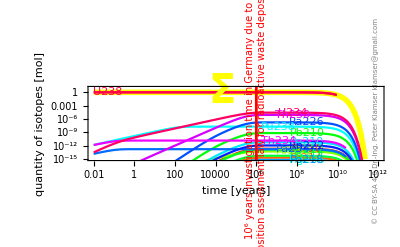
full decay chain of U238
-Graphics-

```mathematica
PlotBateman["U238",{10^-2,10^12}]
(*PlotBateman["Pu236",{10^-3,10^8}]//Timing*)
```

236

4.55156 Minutes calculating decay chain of Pu236

237

19.2987 Minutes calculating decay chain of Pu237

238

123.06 Minutes calculating decay chain of Pu238

239

98.4109 Minutes calculating decay chain of Pu239

240

12.901 Minutes calculating decay chain of Pu240

241

37.863 Minutes calculating decay chain of Pu241

242

304.405 Minutes calculating decay chain of Pu242

243

337.963 Minutes calculating decay chain of Pu243

244

60.9076 Minutes calculating decay chain of Pu244

245

68.0193 Minutes calculating decay chain of Pu245

246

450.521 Minutes calculating decay chain of Pu246

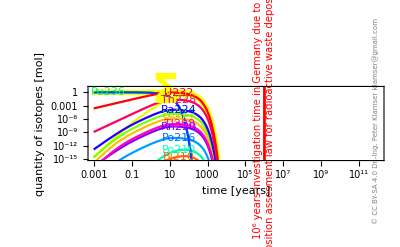
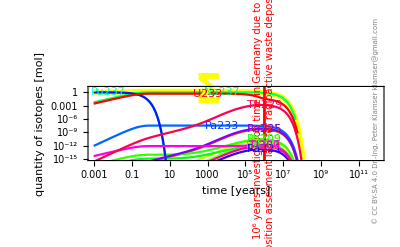
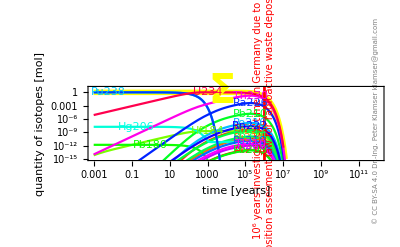
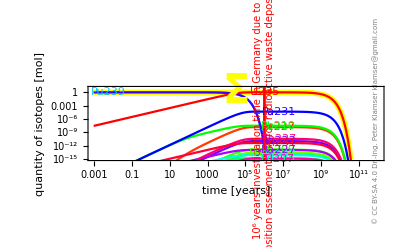
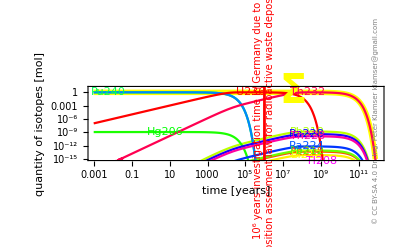
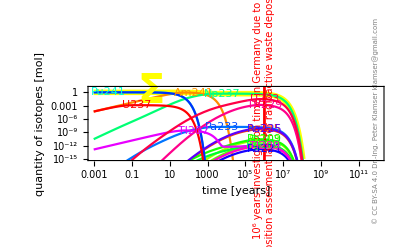
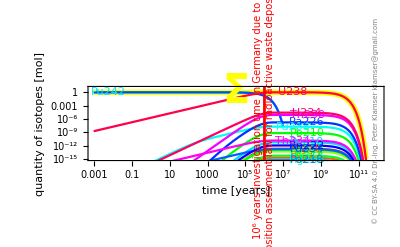
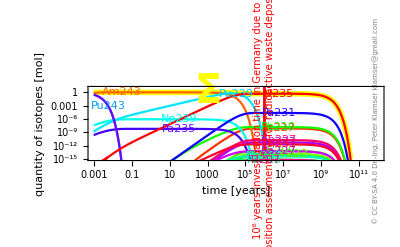
full decay chain of Pu236
-Graphics-
full decay chain of Pu237
-Graphics-
full decay chain of Pu238
-Graphics-
full decay chain of Pu239
-Graphics-
full decay chain of Pu240
-Graphics-
full decay chain of Pu241
-Graphics-
full decay chain of Pu242
-Graphics-
full decay chain of Pu243
-Graphics-
full decay chain of Pu244
-Graphics-
full decay chain of Pu245
-Graphics-
full decay chain of Pu246
-Graphics-

232

3.07969 Minutes calculating decay chain of U232

233

6.13333 Minutes calculating decay chain of U233

234

38.5385 Minutes calculating decay chain of U234

235

71.5682 Minutes calculating decay chain of U235

236

10.7146 Minutes calculating decay chain of U236

237

17.4607 Minutes calculating decay chain of U237

238

244.506 Minutes calculating decay chain of U238

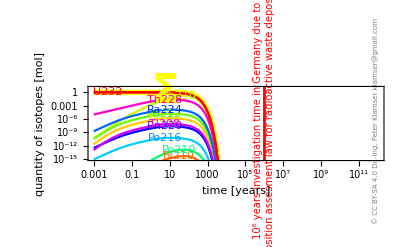
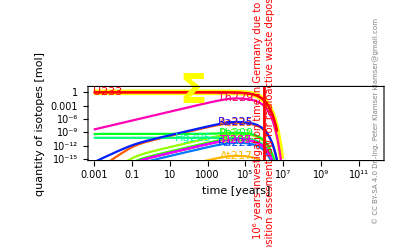
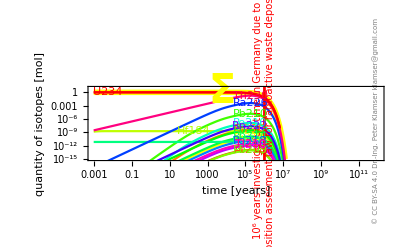
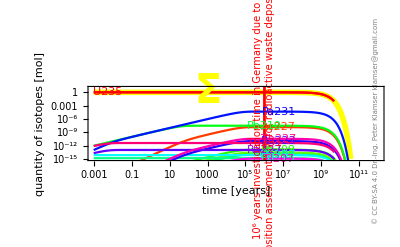
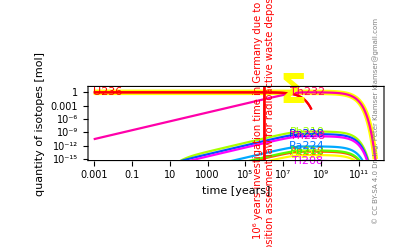
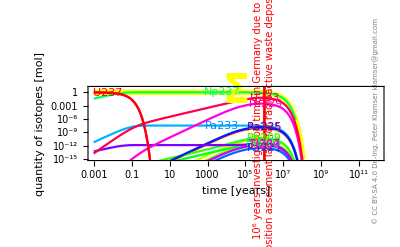
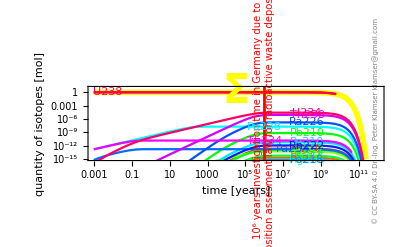
full decay chain of U232
-Graphics-
full decay chain of U233
-Graphics-
full decay chain of U234
-Graphics-
full decay chain of U235
-Graphics-
full decay chain of U236
-Graphics-
full decay chain of U237
-Graphics-
full decay chain of U238
-Graphics-

```mathematica
isotop$nr=235;
Table[isotop$nr++;Print[isotop$nr];PlotBateman["Pu"<>ToString[n],{10^-3,10^12}],{n,236,236+10}]//TableForm

isotop$nr=231;
Table[isotop$nr++;Print[isotop$nr];PlotBateman["U"<>ToString[n],{10^-3,10^12}],{n,232,232+6}]//TableForm
```

```mathematica
Echo[ToString[calculation$time$sum$global]<>" Minutes calculating decay chains"];
```

2117.59 Minutes calculating decay chains

```mathematica
2117.59/60//N
```

35.2932